```mathematica
g[m0_,m_,a1_,a2_,a3_,a4_,a5_,a6_,β_,J_,x_]:=Tanh[β J x  m + (β J x  a1+β J (1-x))  m0 + β J x  a2 m0^2 + β J x  a3 m0^3 + β J x  a4 m0^4+β J x  a5 m0^5 + β J x  a6 m0^6]
```

```mathematica
Ψ1[m_,β_,J_,x_]:=SeriesCoefficient[g[m0,m,a1,a2,a3,a4,a5,a6,β,J,x],{m0,0,1}]
x1[m_,β_,J_,x_]:=a1/. Solve[a1== Ψ1[m,β,J,x],a1]
s1[m_,β_,J_,x_]:=x1[ArcTanh[m]/(β J x),β,J,x][[1]] //Simplify
```

```mathematica
s1[m,β,J,x]
```

(J (-1+m^2) (-1+x) β)/(1+J (-1+m^2) x β)

```mathematica
val[m_,β_,J_,x_]:=(J (-1+m^2) x β)/(-1+J (-1+m^2) (-1+x) β)
```

```mathematica
Ψ2[m_,a1_,β_,J_,x_]:=SeriesCoefficient[g[m0,m,a1,a2,a3,a4,a5,a6,β,J,x],{m0,0,2}]
x2[m_,β_,J_,x_]:=a2/. Solve[a2== Ψ2[ArcTanh[m]/(β J x),s1[m,β,J,x],β,J,x],a2]
s2[m_,β_,J_,x_]:= x2[m,β,J,x][[1]] // Simplify
```

```mathematica
s2[0,1,J,x]
```

0

```mathematica
Ψ3[m_,a1_,a2_,β_,J_,x_]:=SeriesCoefficient[g[m0,m,a1,a2,a3,a4,a5,a6,β,J,x],{m0,0,3}]
x3[m_,β_,J_,x_]:=a3/. Solve[a3== Ψ3[ArcTanh[m]/(β J x),s1[m,β,J,x],s2[m,β,J,x],β,J,x],a3]
s3[m_,β_,J_,x_]:=x3[m,β,J,x][[1]]//Simplify
```

```mathematica
s3[0,β,J,x]
```

(J^3 (-1+x)^3 β^3)/(3 (-1+J x β)^4)

```mathematica
Ψ4[m_,a1_,a2_,a3_,β_,J_,x_]:=SeriesCoefficient[g[m0,m,a1,a2,a3,a4,a5,a6,β,J,x],{m0,0,4}]
x4[m_,β_,J_,x_]:=a4/. Solve[a4== Ψ4[ArcTanh[m]/(β J x),s1[m,β,J,x],s2[m,β,J,x],s3[m,β,J,x],β,J,x],a4]
s4[m_,β_,J_,x_]:=x4[m,β,J,x][[1]] //Simplify
```

```mathematica
s4[0,β,J,x] //Simplify
```

0

```mathematica
Ψ5[m_,a1_,a2_,a3_,a4_,β_,J_,x_]:=SeriesCoefficient[g[m0,m,a1,a2,a3,a4,a5,a6,β,J,x],{m0,0,5}]
x5[m_,β_,J_,x_]:=a5/. Solve[a5== Ψ5[ArcTanh[m]/(β J x),s1[m,β,J,x],s2[m,β,J,x],s3[m,β,J,x],s4[m,β,J,x],β,J,x],a5]
s5[m_,β_,J_,x_]:=x5[m,β,J,x][[1]] //Simplify
```

```mathematica
s5[0,b,J,x] //Simplify
```

(b^5 J^5 (-1+x)^5 (2+3 b J x))/(15 (-1+b J x)^7)

```mathematica
J1[J_,x_,m_,β_]:= J x m
```

```mathematica
J2[J_,x_,m_,β_]:= J (1-x) + J x s1[m,β,J,x]
```

```mathematica
J3[J_,x_,m_,β_]:= J x s2[m,β,J,x]
```

```mathematica
J4[J_,x_,m_,β_]:=  J x s3[m,β,J,x]
```

```mathematica
J6[J_,x_,m_,β_]:=  J x s5[m,β,J,x]
```

```mathematica
J5[J_,x_,m_,β_]:=  J x s4[m,β,J,x]
```

```mathematica
(1-x) J4[1,x,0,1] // Simplify
```

-x/3

```mathematica
(*Plot the renormalized coefficients of the Energy*)
```

```mathematica
Manipulate[Plot[{(1-x) J4[J,x,0,1],(1-x)^2 J6[J,x,0,1],(J2[J,x,0,1])},{x,0,1},GridLines->{{{1-1/J,Dashed}},{{0,Red},{1,Red}}}],{J,0.001,1}]
```

```mathematica
JRR4[J_,x_,β_]:= (1-x) J4[J,x,0,β]
beta4[J_,x_,β_]:= -(1-x)  D[Log[JRR4[J,x,β]],x] //Simplify
beta4[J,x,β]
```

(1+J x^2 β+x (-5+3 J β))/(x (-1+J x β))

```mathematica
JRR6[J_,x_,β_]:= (1-x)^2 J6[J,x,0,β]
beta6[J_,x_,β_]:= -(1-x)  D[Log[JRR6[J,x,β]],x] //Simplify
```

```mathematica
beta2[J_,x_,β_]:= -(1-x) D[Log[J2[J,x,0,β]],x] //Simplify
```

```mathematica
beta2[J,x,1]
```

(-1+J)/(-1+J x)

```mathematica
ϕ6[J_,x_,b_]:=  (  1 +    b^5   J2[J,x,0,b]^5 /(15 b  JRR6[J,x,b]) -  12 /15    b^3 J2[J,x,0,b]^2 JRR4[J,x,b]/(b JRR6[J,x,b]))  2 b J2[J,x,0,b]
```

```mathematica
ϕ4[J_,x_,b_]:= (  1  -    b^3 J2[J,x,0,b]^3/ (  3 b JRR4[J,x,b])) b J2[J,x,0,b] //Simplify
```

```mathematica
beta4[J,x,b]+3(b J2[J,x,0,b]-1)+ϕ4[J,x,b]-2//Simplify
```

0

```mathematica
beta6[J,x,b]+( b J2[J,x,0,b]-1)(5 + 6/5(b JRR4[J,x,b])^2 /(b JRR6[J,x,b]*(b J2[J,x,0,b])^2 ) )+ϕ6[J,x,b]-4  //Simplify
```

0

```mathematica
//Simplify
```

-(2 (-1+b J) x)/((-1+x) (2+3 b J x))

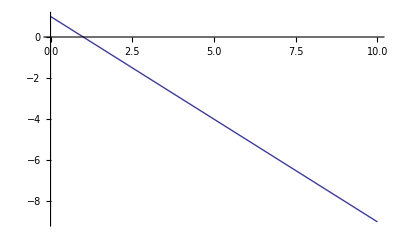

```mathematica
Plot[1-y,{y,0,10}]
```

```mathematica
beta4[z_,y_,β_]:= 2+3 (1- β y) - β y (1-(β y)^3/(3 β z))
```

```mathematica
beta4[z,1,1]
```

1+1/(3 z)

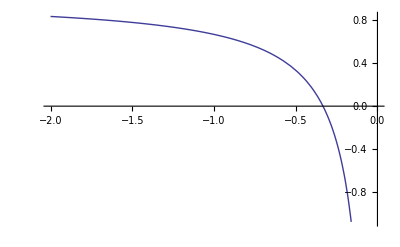

```mathematica
Plot[1+1/(3 z),{z,-2,0}]
```

```mathematica
vectorField=D[-2-3 (1-x)+ x (1-x^3/(3 y)),{{x,y}}]
```

```mathematica
vectorField
```

{4-(4 x^3)/(3 y),x^4/(3 y^2)}

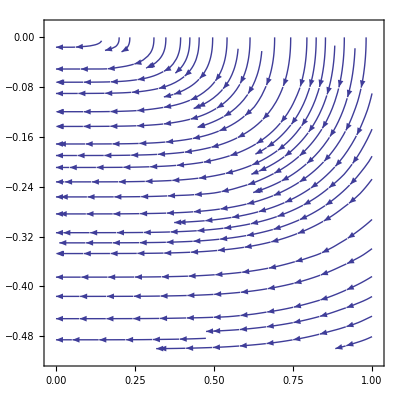

```mathematica
StreamPlot[{-vectorField},{x,0,1},{y,-0.5,0}]
```

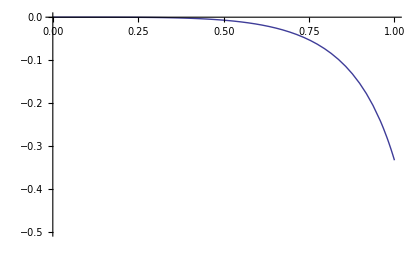

```mathematica
Plot[y^4/(3 (-5+4 y)),{y,0,1},PlotRange->{-0.5,0}]
```

```mathematica
beta6[y_,z_,x_,β_]:= 4+5 (1- β y) -2 β y (1 + 1/15 β^5 y^5/(β x) - 12/15 β^3 y^2 z /(β x))
```

```mathematica
Solve[beta6[y,y^4/(3(4y-5)),x,1]==0,x]//Simplify
```

{{x→(2 y^6)/(3 (45-71 y+28 y^2))}}

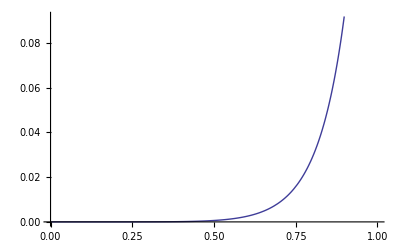

```mathematica
Plot[(2 y^6)/(3 (45-71 y+28 y^2)),{y,0,1}]
```

```mathematica
β J2[J,x,0,β]-β J2[J,x,0,β] β^2 J2[J,x,0,β]^3/(3 J4[J,x,0,β])//Simplify
```

(-1+x)/(x (-1+J x β))

```mathematica
3 (1-β J2[J,x,0,β])-β J2[J,x,0,β] ( 1- β^2 J2[J,x,0,β]^3/(3 J4[J,x,0,β]))//Simplify
```

(1+x (-4+3 J β))/(x (-1+J x β))

```mathematica
f[m0_,J_,x_,β_]:=-J1[J,x,sol[J,x,β],β]  m0+(1/2-J2[J,x,sol[J,x,β],β]/2)  m0^2 +(-J3[J,x,sol[J,x,β],β]/3) m0^3+(1./12-J4[J,x,sol[J,x,β],β]/4)   m0^4
```

```mathematica
f[m0,1.1,1-x,1]
```

```mathematica
s1[0]  m0+s2[0]  m0^2 + s3[0]  m0^3 + s4[0]  m0^4 + s5[0]m0^5 + s6[0] m0^6
```

```mathematica
mhat[J (1-x), J x,1,m0,sol1[1,J,x]]
```

```mathematica
energy[m0_,m_]:=  -g / (2 β) m0^2+alpha^2/(2 g β) f[m0,m]^2 + alpha/( 2 β g) Log[1-f[m0,m]^2] - alpha/ (g β) Log[2]
```

```mathematica
Series[energy[m0,0],{m0,0,6}]
```

-(alpha Log[2])/(g β)+(g m0^2)/(2 (-1+alpha) β)+(alpha g^3 m0^4)/(12 (-1+alpha)^4 β)+((2 alpha+3 alpha^2) g^5 m0^6)/(90 (-1+alpha)^7 β)+O[m0]^7

```mathematica
s[m0_]:= - Log[(1-m0^2)/4]/2-m0/2 Log[(1+m0)/(1-m0)]
```

```mathematica
Series[s[m0],{m0,0,6}]
```

Log[4]/2-m0^2/2-m0^4/12-m0^6/30+O[m0]^7

```mathematica
free[m0_,m_] :=energy[m0,m]-s[m0]/β
```

```mathematica
(*Calcola Free energy m=0*)
```

```mathematica
D[free[m0,0],m0] // Simplify
```

1/(2 β)(-2 g m0+1/(15 (-1+alpha)^7)2 alpha^2 m0 (-15 (-1+alpha)^6-5 (-1+alpha)^3 g^2 m0^2-(2+3 alpha) g^4 m0^4) (-g/(-1+alpha)-(g^3 m0^2)/(-1+alpha)^4-((2+3 alpha) g^5 m0^4)/(3 (-1+alpha)^7))-(2 alpha m0 (-15 (-1+alpha)^6-5 (-1+alpha)^3 g^2 m0^2-(2+3 alpha) g^4 m0^4) (-g/(-1+alpha)-(g^3 m0^2)/(-1+alpha)^4-((2+3 alpha) g^5 m0^4)/(3 (-1+alpha)^7)))/(15 (-1+alpha)^7 (1-(g^2 m0^2 (15 (-1+alpha)^6+5 (-1+alpha)^3 g^2 m0^2+(2+3 alpha) g^4 m0^4)^2)/(225 (-1+alpha)^14)))+Log[(1+m0)/(1-m0)])

```mathematica
prova[alpha_,g_,β_,m0_]:=1/(2 β)(-2 g m0+1/(15 (-1+alpha)^7)2 alpha^2 m0 (-15 (-1+alpha)^6-5 (-1+alpha)^3 g^2 m0^2-(2+3 alpha) g^4 m0^4) (-g/(-1+alpha)-(g^3 m0^2)/(-1+alpha)^4-((2+3 alpha) g^5 m0^4)/(3 (-1+alpha)^7))-(2 alpha m0 (-15 (-1+alpha)^6-5 (-1+alpha)^3 g^2 m0^2-(2+3 alpha) g^4 m0^4) (-g/(-1+alpha)-(g^3 m0^2)/(-1+alpha)^4-((2+3 alpha) g^5 m0^4)/(3 (-1+alpha)^7)))/(15 (-1+alpha)^7 (1-(g^2 m0^2 (15 (-1+alpha)^6+5 (-1+alpha)^3 g^2 m0^2+(2+3 alpha) g^4 m0^4)^2)/(225 (-1+alpha)^14)))
```

```mathematica
Series[prova[J (1-x),J x, 1, m0],{m0,0,3}]//Simplify
```

((1-J) m0)/(1+J (-1+x))+((1+4 J (-1+x)+6 J^2 (-1+x)^2+4 J^3 (-1+x)^3+J^4 (1-4 x+6 x^2-3 x^3)) m0^3)/(3 (1+J (-1+x))^4)+O[m0]^4

```mathematica
Series[free[m0,0],{m0,0,6}]
```

(-(alpha Log[2])/(g β)-Log[4]/(2 β))+((-1+alpha+g) m0^2)/(2 (-1+alpha) β)+((1-4 alpha+6 alpha^2-4 alpha^3+alpha^4+alpha g^3) m0^4)/(12 (-1+alpha)^4 β)+(1/(30 β)-(alpha g^5)/(45 (-1+alpha)^8 β)-(alpha^2 g^5)/(90 (-1+alpha)^8 β)+(alpha^3 g^5)/(30 (-1+alpha)^8 β)) m0^6+O[m0]^7

```mathematica
appoggio1[alpha_,g_,β_,m0_]:=(-(alpha Log[2])/(g β)-Log[4]/(2 β))+((-1+alpha+g) m0^2)/(2 (-1+alpha) β)+((1-4 alpha+6 alpha^2-4 alpha^3+alpha^4+alpha g^3) m0^4)/(12 (-1+alpha)^4 β)+(1/(30 β)-(alpha g^5)/(45 (-1+alpha)^8 β)-(alpha^2 g^5)/(90 (-1+alpha)^8 β)+(alpha^3 g^5)/(30 (-1+alpha)^8 β)) m0^6
```

```mathematica
sesto[alpha_,g_,β_]:=(1/(30 β)+(alpha g^5 x)/(45 (-1+alpha)^7 β)+(alpha^2 g^5 x)/(30 (-1+alpha)^7 β))
```

```mathematica
sesto[(1-x),x,1]  //Simplify
```

-(5-11 x+3 x^2)/(90 x)

```mathematica
FreeEnergy[m0_,x_,β_,J_]:=appoggio1[β J (1-x),β J x, β,m0]
```

```mathematica
FreeEnergy[m0,1,1,1] // Simplify
```

1/60 (5 m0^4+2 m0^6-60 Log[2])

```mathematica
δ0[β_,x_]:=SeriesCoefficient[FreeEnergy[m0,x,β,J],{m0,0,0}]
δ2[x_,J_,β_]:=SeriesCoefficient[FreeEnergy[m0,x,β,J],{m0,0,2}]
δ4[x_,J_,β_]:=SeriesCoefficient[FreeEnergy[m0,x,β,J],{m0,0,4}]
δ6[x_,J_,β_]:=SeriesCoefficient[FreeEnergy[m0,x,β,J],{m0,0,6}]
```

```mathematica
δ6[x,1,1] //Simplify
```

(-5+8 x)/(90 x^2)

```mathematica
(-5+8 x)/(90 x)
```

(-5+8 x)/(90 x)

```mathematica
Solve[δ4[x,1.01,1] == 0,{x,J}, Reals]
```

{{x→-0.00303299}}

```mathematica
Limit[δ6[x,1,1] δ2[x,J,1],x-> 0]
```

(1-J) DirectedInfinity[1/Sign[-1+J]]

```mathematica
s1[0]
```

-g/(-1+alpha)

```mathematica
Manipulate[ Plot[{ δ2[x,J,1], δ4[x,J,1], δ6[x,J,1] },{x,0,1}, GridLines->{{{1-1/J,Dashed}},{{0,Red},{1,Orange}}},PlotRange -> {}],{J,0.001,1.2}  ]
```

Plot::prng: Value of option PlotRange -> {} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Manipulate[ Plot[δ0[x,1]+m^2 δ2[x,J,1]+ m^4 δ4[x,J,1],{m,-1,1}],{J,0.01,1.3},{x,0.01,1}]
```

```mathematica
(*La Funzione e' sempre a concavita' positiva intorno a m=0. Per valori J<1 per J>1 ha una transizione del secondo ordine. Tutto e' abbastanza smooth e i coefficienti del secondo e quarto ordine vengono rinormalizzati molto poco *)
```

```mathematica
Series[energy[m0,0],{m0,0,6}]
```

-(alpha Log[2])/(g β)+(g m0^2)/(2 (-1+alpha) β)+(alpha g^3 m0^4)/(12 (-1+alpha)^4 β)+((2 alpha+3 alpha^2) g^5 m0^6)/(90 (-1+alpha)^7 β)+O[m0]^7

```mathematica
appoggio[alpha_,g_,β_,m0_]:=-(alpha Log[2])/(g β)+(g m0^2)/(2 (-1+alpha) β)+(alpha g^3 m0^4)/(12 (-1+alpha)^4 β)+((2 alpha+3 alpha^2) g^5 m0^6)/(90 (-1+alpha)^7 β)
```

```mathematica
Energy[m0_,x_,β_,J_]:=appoggio[β J (1-x),β J x, β,m0]
```

```mathematica
J0[β_,x_]:=SeriesCoefficient[-Energy[m0,x,β,J],{m0,0,0}]
J2[x_,J_,β_]:=SeriesCoefficient[-Energy[m0,x,β,J],{m0,0,2}]
J4[x_,J_,β_]:=SeriesCoefficient[-Energy[m0,x,β,J],{m0,0,4}]
J6[x_,J_,β_]:=SeriesCoefficient[-Energy[m0,x,β,J],{m0,0,6}]
```

```mathematica
Manipulate[ Plot[{2*J2[x,J,1]/J ,J4[x,J,1],J6[x,J,1]},{x,0,1}, GridLines->{{{1-1/J,Dashed}},{{0,Red},{1,Red}}}],{J,0.001,1.2}]
```

```mathematica
Energy[m0_,x_,β_,J_]:=appoggio[β J (1-x),β J x, β,m0]
```

```mathematica
Simplify[Series[Energy[m0,x,β,J],{m0,0,4}]]
```

((-1+x) Log[2])/(x β)-(J x m0^2)/(2+2 J (-1+x) β)-((J^4 (-1+x) x^3 β^3) m0^4)/(12 (1+J (-1+x) β)^4)+O[m0]^5

```mathematica
Jnew[x_,β_,J_]:=-(J x)/(2+2 J (-1+x) β)
```

```mathematica
J4new[x_,β_,J_]:=+(7 J^4 (-1+x) x^3 β^3)/(12 (1+J (-1+x) β)^4)
```

```mathematica
Manipulate[Plot[{-2 Jnew[x,1,J]/J/J4new[x,1,J]},{x,0,1}, GridLines->{{1-1/J},{}}],{J,0.001,1.3}]
```

```mathematica
(*Calcola Free energy m/=0*)
```

```mathematica
Series[free[m0,m],{m0,0,4}]
```

(alpha^2 m^2-2 alpha Log[2]-g Log[4]+alpha Log[1-m^2])/(2 g β)-(alpha m m0)/β+((1-alpha-g+alpha m^2) m0^2)/(2 (1-alpha+alpha m^2) β)+(-(alpha g^2 m (3 alpha-3 alpha^2+2 m^2-7 alpha m^2+5 alpha^2 m^2-2 m^4+3 alpha m^4-alpha^2 m^4+alpha m^6-alpha^2 m^6+2 Sech[alpha m]^4-2 alpha Sech[alpha m]^4+2 alpha m^2 Sech[alpha m]^4-Cosh[2 alpha m] Sech[alpha m]^4+alpha Cosh[2 alpha m] Sech[alpha m]^4-alpha m^2 Cosh[2 alpha m] Sech[alpha m]^4-3 alpha m Sech[alpha m]^4 Sinh[2 alpha m]+3 alpha m^3 Sech[alpha m]^4 Sinh[2 alpha m]+3 alpha^2 Tanh[alpha m]^2+2 alpha m^2 Tanh[alpha m]^2-5 alpha^2 m^2 Tanh[alpha m]^2-2 alpha m^4 Tanh[alpha m]^2+alpha^2 m^4 Tanh[alpha m]^2+alpha^2 m^6 Tanh[alpha m]^2))/(3 (-1+m^2) (1-alpha+alpha m^2)^4 β (1-alpha+alpha Tanh[alpha m]^2))+1/(2 g β)alpha^2 ((2 g^2 m (-1+m^2) (g-g m^2))/((1+alpha (-1+m^2))^4)-(2 g^3 m Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2)))) m0^3+(1/(12 β)+1/(2 g β)alpha^2 ((g^4 m^2 (-1+m^2)^2)/((1+alpha (-1+m^2))^6)-(g^4 m Sech[alpha m]^7 (-24 alpha m (-1+m^2) (-2+alpha (3-2 m^2)+alpha^2 (-1+m^2)) Cosh[alpha m]-6 alpha m (-1+m^2) (-1-alpha (-5+m^2)+4 alpha^2 (-1+m^2)) Cosh[3 alpha m]+6 alpha m Cosh[5 alpha m]-6 alpha^2 m Cosh[5 alpha m]-6 alpha m^3 Cosh[5 alpha m]+12 alpha^2 m^3 Cosh[5 alpha m]-6 alpha^2 m^5 Cosh[5 alpha m]-10 Sinh[alpha m]-16 alpha Sinh[alpha m]+62 alpha^2 Sinh[alpha m]-36 alpha^3 Sinh[alpha m]-20 alpha m^2 Sinh[alpha m]-46 alpha^2 m^2 Sinh[alpha m]+60 alpha^3 m^2 Sinh[alpha m]-22 alpha^2 m^4 Sinh[alpha m]-12 alpha^3 m^4 Sinh[alpha m]+6 alpha^2 m^6 Sinh[alpha m]-12 alpha^3 m^6 Sinh[alpha m]-9 Sinh[3 alpha m]+30 alpha Sinh[3 alpha m]-33 alpha^2 Sinh[3 alpha m]+12 alpha^3 Sinh[3 alpha m]-18 alpha m^2 Sinh[3 alpha m]+51 alpha^2 m^2 Sinh[3 alpha m]-36 alpha^3 m^2 Sinh[3 alpha m]-27 alpha^2 m^4 Sinh[3 alpha m]+36 alpha^3 m^4 Sinh[3 alpha m]+9 alpha^2 m^6 Sinh[3 alpha m]-12 alpha^3 m^6 Sinh[3 alpha m]+Sinh[5 alpha m]-2 alpha Sinh[5 alpha m]+alpha^2 Sinh[5 alpha m]+2 alpha m^2 Sinh[5 alpha m]+alpha^2 m^2 Sinh[5 alpha m]-5 alpha^2 m^4 Sinh[5 alpha m]+3 alpha^2 m^6 Sinh[5 alpha m]))/(24 (1+alpha (-1+m^2))^6 (1-alpha+alpha Tanh[alpha m]^2)^2)-(2 g^3 (g-g m^2) Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^5 (1-alpha+alpha Tanh[alpha m]^2)))+1/(8 g β)alpha (1/(1-m^2)2 (-(2 g^2 m^2)/((1-m^2) (1+alpha (-1+m^2))^3)+(2 g^2 m^4)/((1-m^2) (1+alpha (-1+m^2))^3)+(4 g^2 m^2)/((1-m^2)^2 (1+alpha (-1+m^2))^2)-(8 g^2 m^4)/((1-m^2)^2 (1+alpha (-1+m^2))^2)+(4 g^2 m^6)/((1-m^2)^2 (1+alpha (-1+m^2))^2)+g^2/((1-m^2) (1+alpha (-1+m^2))^2)-(2 g^2 m^2)/((1-m^2) (1+alpha (-1+m^2))^2)+(g^2 m^4)/((1-m^2) (1+alpha (-1+m^2))^2)) (-(2 g^2 m^2 (-1+m^2))/((1+alpha (-1+m^2))^3)-((g-g m^2)^2)/((1+alpha (-1+m^2))^2))-(2 m (g-g m^2) (-(8 g^3 m^3)/((1-m^2)^2 (1+alpha (-1+m^2))^4)+(16 g^3 m^5)/((1-m^2)^2 (1+alpha (-1+m^2))^4)-(8 g^3 m^7)/((1-m^2)^2 (1+alpha (-1+m^2))^4)-(2 g^3 m)/((1-m^2) (1+alpha (-1+m^2))^4)+(4 g^3 m^3)/((1-m^2) (1+alpha (-1+m^2))^4)-(2 g^3 m^5)/((1-m^2) (1+alpha (-1+m^2))^4)+(8 g^3 m^3)/((1-m^2)^3 (1+alpha (-1+m^2))^3)-(24 g^3 m^5)/((1-m^2)^3 (1+alpha (-1+m^2))^3)+(24 g^3 m^7)/((1-m^2)^3 (1+alpha (-1+m^2))^3)-(8 g^3 m^9)/((1-m^2)^3 (1+alpha (-1+m^2))^3)+(4 g^3 m)/((1-m^2)^2 (1+alpha (-1+m^2))^3)-(12 g^3 m^3)/((1-m^2)^2 (1+alpha (-1+m^2))^3)+(12 g^3 m^5)/((1-m^2)^2 (1+alpha (-1+m^2))^3)-(4 g^3 m^7)/((1-m^2)^2 (1+alpha (-1+m^2))^3)-(4 g^3 m Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(4 alpha g^3 m Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))-(4 alpha g^3 m^3 Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(2 g^3 m Cosh[2 alpha m] Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))-(2 alpha g^3 m Cosh[2 alpha m] Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(2 alpha g^3 m^3 Cosh[2 alpha m] Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(2 alpha g^3 m^2 Sech[alpha m]^4 Sinh[2 alpha m])/((1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))-(2 alpha g^3 m^4 Sech[alpha m]^4 Sinh[2 alpha m])/((1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))))/((1-m^2) (1+alpha (-1+m^2)))+1/(1-m^2)4 (-(g^4 m^2 (-1+m^2)^2)/((1+alpha (-1+m^2))^6)+(g^4 m Sech[alpha m]^7 (-24 alpha m (-1+m^2) (-2+alpha (3-2 m^2)+alpha^2 (-1+m^2)) Cosh[alpha m]-6 alpha m (-1+m^2) (-1-alpha (-5+m^2)+4 alpha^2 (-1+m^2)) Cosh[3 alpha m]+6 alpha m Cosh[5 alpha m]-6 alpha^2 m Cosh[5 alpha m]-6 alpha m^3 Cosh[5 alpha m]+12 alpha^2 m^3 Cosh[5 alpha m]-6 alpha^2 m^5 Cosh[5 alpha m]-10 Sinh[alpha m]-16 alpha Sinh[alpha m]+62 alpha^2 Sinh[alpha m]-36 alpha^3 Sinh[alpha m]-20 alpha m^2 Sinh[alpha m]-46 alpha^2 m^2 Sinh[alpha m]+60 alpha^3 m^2 Sinh[alpha m]-22 alpha^2 m^4 Sinh[alpha m]-12 alpha^3 m^4 Sinh[alpha m]+6 alpha^2 m^6 Sinh[alpha m]-12 alpha^3 m^6 Sinh[alpha m]-9 Sinh[3 alpha m]+30 alpha Sinh[3 alpha m]-33 alpha^2 Sinh[3 alpha m]+12 alpha^3 Sinh[3 alpha m]-18 alpha m^2 Sinh[3 alpha m]+51 alpha^2 m^2 Sinh[3 alpha m]-36 alpha^3 m^2 Sinh[3 alpha m]-27 alpha^2 m^4 Sinh[3 alpha m]+36 alpha^3 m^4 Sinh[3 alpha m]+9 alpha^2 m^6 Sinh[3 alpha m]-12 alpha^3 m^6 Sinh[3 alpha m]+Sinh[5 alpha m]-2 alpha Sinh[5 alpha m]+alpha^2 Sinh[5 alpha m]+2 alpha m^2 Sinh[5 alpha m]+alpha^2 m^2 Sinh[5 alpha m]-5 alpha^2 m^4 Sinh[5 alpha m]+3 alpha^2 m^6 Sinh[5 alpha m]))/(24 (1+alpha (-1+m^2))^6 (1-alpha+alpha Tanh[alpha m]^2)^2)+(2 g^3 (g-g m^2) Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^5 (1-alpha+alpha Tanh[alpha m]^2)))+1/(1-m^2)3 ((2 g m)/((1-m^2) (1+alpha (-1+m^2)))-(2 g m^3)/((1-m^2) (1+alpha (-1+m^2)))) (-(2 g^2 m (-1+m^2) (g-g m^2))/((1+alpha (-1+m^2))^4)+(2 g^3 m Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))))) m0^4+O[m0]^5

```mathematica
app[m_,alpha_, g_,β_]:=(alpha^2 m^2-2 alpha Log[2]-g Log[4]+alpha Log[1-m^2])/(2 g β)-(alpha m m0)/β+((1-alpha-g+alpha m^2) m0^2)/(2 (1-alpha+alpha m^2) β)+(-(alpha g^2 m (3 alpha-3 alpha^2+2 m^2-7 alpha m^2+5 alpha^2 m^2-2 m^4+3 alpha m^4-alpha^2 m^4+alpha m^6-alpha^2 m^6+2 Sech[alpha m]^4-2 alpha Sech[alpha m]^4+2 alpha m^2 Sech[alpha m]^4-Cosh[2 alpha m] Sech[alpha m]^4+alpha Cosh[2 alpha m] Sech[alpha m]^4-alpha m^2 Cosh[2 alpha m] Sech[alpha m]^4-3 alpha m Sech[alpha m]^4 Sinh[2 alpha m]+3 alpha m^3 Sech[alpha m]^4 Sinh[2 alpha m]+3 alpha^2 Tanh[alpha m]^2+2 alpha m^2 Tanh[alpha m]^2-5 alpha^2 m^2 Tanh[alpha m]^2-2 alpha m^4 Tanh[alpha m]^2+alpha^2 m^4 Tanh[alpha m]^2+alpha^2 m^6 Tanh[alpha m]^2))/(3 (-1+m^2) (1-alpha+alpha m^2)^4 β (1-alpha+alpha Tanh[alpha m]^2))+1/(2 g β)alpha^2 ((2 g^2 m (-1+m^2) (g-g m^2))/((1+alpha (-1+m^2))^4)-(2 g^3 m Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2)))) m0^3+(1/(12 β)+1/(2 g β)alpha^2 ((g^4 m^2 (-1+m^2)^2)/((1+alpha (-1+m^2))^6)-(g^4 m Sech[alpha m]^7 (-24 alpha m (-1+m^2) (-2+alpha (3-2 m^2)+alpha^2 (-1+m^2)) Cosh[alpha m]-6 alpha m (-1+m^2) (-1-alpha (-5+m^2)+4 alpha^2 (-1+m^2)) Cosh[3 alpha m]+6 alpha m Cosh[5 alpha m]-6 alpha^2 m Cosh[5 alpha m]-6 alpha m^3 Cosh[5 alpha m]+12 alpha^2 m^3 Cosh[5 alpha m]-6 alpha^2 m^5 Cosh[5 alpha m]-10 Sinh[alpha m]-16 alpha Sinh[alpha m]+62 alpha^2 Sinh[alpha m]-36 alpha^3 Sinh[alpha m]-20 alpha m^2 Sinh[alpha m]-46 alpha^2 m^2 Sinh[alpha m]+60 alpha^3 m^2 Sinh[alpha m]-22 alpha^2 m^4 Sinh[alpha m]-12 alpha^3 m^4 Sinh[alpha m]+6 alpha^2 m^6 Sinh[alpha m]-12 alpha^3 m^6 Sinh[alpha m]-9 Sinh[3 alpha m]+30 alpha Sinh[3 alpha m]-33 alpha^2 Sinh[3 alpha m]+12 alpha^3 Sinh[3 alpha m]-18 alpha m^2 Sinh[3 alpha m]+51 alpha^2 m^2 Sinh[3 alpha m]-36 alpha^3 m^2 Sinh[3 alpha m]-27 alpha^2 m^4 Sinh[3 alpha m]+36 alpha^3 m^4 Sinh[3 alpha m]+9 alpha^2 m^6 Sinh[3 alpha m]-12 alpha^3 m^6 Sinh[3 alpha m]+Sinh[5 alpha m]-2 alpha Sinh[5 alpha m]+alpha^2 Sinh[5 alpha m]+2 alpha m^2 Sinh[5 alpha m]+alpha^2 m^2 Sinh[5 alpha m]-5 alpha^2 m^4 Sinh[5 alpha m]+3 alpha^2 m^6 Sinh[5 alpha m]))/(24 (1+alpha (-1+m^2))^6 (1-alpha+alpha Tanh[alpha m]^2)^2)-(2 g^3 (g-g m^2) Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^5 (1-alpha+alpha Tanh[alpha m]^2)))+1/(8 g β)alpha (1/(1-m^2)2 (-(2 g^2 m^2)/((1-m^2) (1+alpha (-1+m^2))^3)+(2 g^2 m^4)/((1-m^2) (1+alpha (-1+m^2))^3)+(4 g^2 m^2)/((1-m^2)^2 (1+alpha (-1+m^2))^2)-(8 g^2 m^4)/((1-m^2)^2 (1+alpha (-1+m^2))^2)+(4 g^2 m^6)/((1-m^2)^2 (1+alpha (-1+m^2))^2)+g^2/((1-m^2) (1+alpha (-1+m^2))^2)-(2 g^2 m^2)/((1-m^2) (1+alpha (-1+m^2))^2)+(g^2 m^4)/((1-m^2) (1+alpha (-1+m^2))^2)) (-(2 g^2 m^2 (-1+m^2))/((1+alpha (-1+m^2))^3)-((g-g m^2)^2)/((1+alpha (-1+m^2))^2))-(2 m (g-g m^2) (-(8 g^3 m^3)/((1-m^2)^2 (1+alpha (-1+m^2))^4)+(16 g^3 m^5)/((1-m^2)^2 (1+alpha (-1+m^2))^4)-(8 g^3 m^7)/((1-m^2)^2 (1+alpha (-1+m^2))^4)-(2 g^3 m)/((1-m^2) (1+alpha (-1+m^2))^4)+(4 g^3 m^3)/((1-m^2) (1+alpha (-1+m^2))^4)-(2 g^3 m^5)/((1-m^2) (1+alpha (-1+m^2))^4)+(8 g^3 m^3)/((1-m^2)^3 (1+alpha (-1+m^2))^3)-(24 g^3 m^5)/((1-m^2)^3 (1+alpha (-1+m^2))^3)+(24 g^3 m^7)/((1-m^2)^3 (1+alpha (-1+m^2))^3)-(8 g^3 m^9)/((1-m^2)^3 (1+alpha (-1+m^2))^3)+(4 g^3 m)/((1-m^2)^2 (1+alpha (-1+m^2))^3)-(12 g^3 m^3)/((1-m^2)^2 (1+alpha (-1+m^2))^3)+(12 g^3 m^5)/((1-m^2)^2 (1+alpha (-1+m^2))^3)-(4 g^3 m^7)/((1-m^2)^2 (1+alpha (-1+m^2))^3)-(4 g^3 m Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(4 alpha g^3 m Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))-(4 alpha g^3 m^3 Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(2 g^3 m Cosh[2 alpha m] Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))-(2 alpha g^3 m Cosh[2 alpha m] Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(2 alpha g^3 m^3 Cosh[2 alpha m] Sech[alpha m]^4)/(3 (1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))+(2 alpha g^3 m^2 Sech[alpha m]^4 Sinh[2 alpha m])/((1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))-(2 alpha g^3 m^4 Sech[alpha m]^4 Sinh[2 alpha m])/((1-m^2) (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))))/((1-m^2) (1+alpha (-1+m^2)))+1/(1-m^2)4 (-(g^4 m^2 (-1+m^2)^2)/((1+alpha (-1+m^2))^6)+(g^4 m Sech[alpha m]^7 (-24 alpha m (-1+m^2) (-2+alpha (3-2 m^2)+alpha^2 (-1+m^2)) Cosh[alpha m]-6 alpha m (-1+m^2) (-1-alpha (-5+m^2)+4 alpha^2 (-1+m^2)) Cosh[3 alpha m]+6 alpha m Cosh[5 alpha m]-6 alpha^2 m Cosh[5 alpha m]-6 alpha m^3 Cosh[5 alpha m]+12 alpha^2 m^3 Cosh[5 alpha m]-6 alpha^2 m^5 Cosh[5 alpha m]-10 Sinh[alpha m]-16 alpha Sinh[alpha m]+62 alpha^2 Sinh[alpha m]-36 alpha^3 Sinh[alpha m]-20 alpha m^2 Sinh[alpha m]-46 alpha^2 m^2 Sinh[alpha m]+60 alpha^3 m^2 Sinh[alpha m]-22 alpha^2 m^4 Sinh[alpha m]-12 alpha^3 m^4 Sinh[alpha m]+6 alpha^2 m^6 Sinh[alpha m]-12 alpha^3 m^6 Sinh[alpha m]-9 Sinh[3 alpha m]+30 alpha Sinh[3 alpha m]-33 alpha^2 Sinh[3 alpha m]+12 alpha^3 Sinh[3 alpha m]-18 alpha m^2 Sinh[3 alpha m]+51 alpha^2 m^2 Sinh[3 alpha m]-36 alpha^3 m^2 Sinh[3 alpha m]-27 alpha^2 m^4 Sinh[3 alpha m]+36 alpha^3 m^4 Sinh[3 alpha m]+9 alpha^2 m^6 Sinh[3 alpha m]-12 alpha^3 m^6 Sinh[3 alpha m]+Sinh[5 alpha m]-2 alpha Sinh[5 alpha m]+alpha^2 Sinh[5 alpha m]+2 alpha m^2 Sinh[5 alpha m]+alpha^2 m^2 Sinh[5 alpha m]-5 alpha^2 m^4 Sinh[5 alpha m]+3 alpha^2 m^6 Sinh[5 alpha m]))/(24 (1+alpha (-1+m^2))^6 (1-alpha+alpha Tanh[alpha m]^2)^2)+(2 g^3 (g-g m^2) Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^5 (1-alpha+alpha Tanh[alpha m]^2)))+1/(1-m^2)3 ((2 g m)/((1-m^2) (1+alpha (-1+m^2)))-(2 g m^3)/((1-m^2) (1+alpha (-1+m^2)))) (-(2 g^2 m (-1+m^2) (g-g m^2))/((1+alpha (-1+m^2))^4)+(2 g^3 m Sech[alpha m]^4 (2-2 alpha+2 alpha m^2+(-1+alpha-alpha m^2) Cosh[2 alpha m]+3 alpha m (-1+m^2) Sinh[2 alpha m]))/(3 (1+alpha (-1+m^2))^4 (1-alpha+alpha Tanh[alpha m]^2))))) m0^4
```

```mathematica
FreeEnBT[m0_,β_,J_,x_,m_]:=app[m,β J (1-x), β J x, β]
sol1[β_,J_,x_]:= √((3 (β J (1-x)-1))/(β J (1-x))^3)
```

```mathematica
sol1[1.,1.3,.2]
```

0.326618

```mathematica
χ0[J_,x_,β_]:=SeriesCoefficient[FreeEnBT[m0,β,J,x,sol1[β,J,x]],{m0,0,0}]
χ1[J_,x_,β_]:=SeriesCoefficient[FreeEnBT[m0,β,J,x,sol1[β,J,x]],{m0,0,1}]
χ2[J_,x_,β_]:=SeriesCoefficient[FreeEnBT[m0,β,J,x,sol1[β,J,x]],{m0,0,2}]
χ3[J_,x_,β_]:=SeriesCoefficient[FreeEnBT[m0,β,J,x,sol1[β,J,x]],{m0,0,3}]
χ4[J_,x_,β_]:=SeriesCoefficient[FreeEnBT[m0,β,J,x,sol1[β,J,x]],{m0,0,4}]
```

```mathematica
Limit[χ2[1.2,0.1,1],x -> 0]
```

0.0229058

```mathematica
χ0[1.2,x,1]+m0 χ1[1.2,x,1]+m0^2 χ2[1.2,x,1] + m0^3 χ3[1.2,x,1]+m0^4 χ4[ 1.2,x,1]
```

```mathematica
χ2[1.2,x,1]
```

-(0.0833333 (-1.08333+10.5 x+1. x^2))/(0.180556-0.75 x-2.16667 x^2+1. x^3)

```mathematica
χ0[1.2,x,1]
```

(0.416667 ((2.5 (-1+1.2 (1-x)))/(1-x)-1.66355 (1-x)-1.66355 x+1.2 (1-x) Log[1-(1.73611 (-1+1.2 (1-x)))/(1-x)^3]))/x

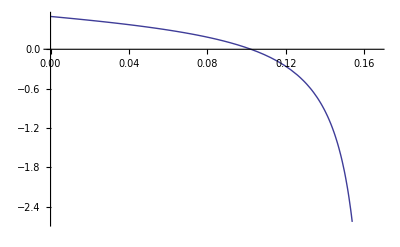

```mathematica
Plot[-(0.08333333333333331 (-1.083333333333333+10.5 x+1. x^2))/(0.18055555555555547-0.7499999999999998 x-2.1666666666666665 x^2+1. x^3),{x,0,1-1/1.2}]
```

```mathematica
χ4[1.2,x,1]
```

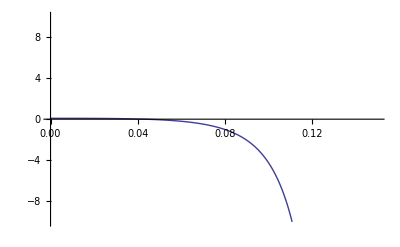

```mathematica
Plot[%19,{x,0.,.15},PlotRange->{-10,10}]
```

```mathematica
FreEn[x_,J_,m0_]:= χ0[J,x,1]+m0 χ1[J,x,1]+m0^2 χ2[J,x,1] + m0^3 χ3[J,x,1]+m0^4 χ4[J,x,1]
```

```mathematica
Manipulate[Plot[χ0[1.2,x,1]+m0 χ1[1.2,x,1],{m0,-1,1}],{x,0.01,1-1/1.2}]
```

```mathematica
FreEn[x,1.3,m0]
```